```mathematica
ClearAll["Global`*"];
Q=0.2;
sth=0.01;                     (*√θ=0.1*)
(*Paramètres critiques déformés (Table 2)*)
rhoC=0.49810;
TC=0.21210;
PC=0.079624;

(*-----Fonctions pour le cas déformé-----*)
rθ[r_,s_]:=(2 r/Pi) ArcTan[r/Sqrt[s]];
drθ[r_,s_]:=2/Pi (ArcTan[r/Sqrt[s]]+(r s)/(r^2+s^2));
μ[r_,s_]:=(2/Pi) (ArcTan[r/Sqrt[s]]-(r s)/(r^2+s^2));
Qθ[r_,s_]:=Q μ[r,s];
dQθ[r_,s_]:=(4 Q r^2 Sqrt[s])/(Pi (r^2+s)^2);
χ[r_,s_]:=dQθ[r,s]/drθ[r,s];
ρ[r_,s_]:=rθ[r,s];

(*Equation d'état exacte (53)*)
Pexact[r_,T_,s_]:=Module[{ρh=ρ[r,s],Qh=Qθ[r,s],chi=χ[r,s]},T/(2 ρh)-1/(8 Pi ρh^2)+Qh^2/(8 Pi ρh^4)-(Qh chi)/(4 Pi ρh^3)];

(*Cas commutatif (θ=0)*)
Pcom[r_,T_]:=T/(2 r)-1/(8 Pi r^2)+Q^2/(8 Pi r^4);

(*-----Isothermes-----*)
Tlist={0.9 TC,TC,1.1 TC,1.3 TC};
colors={Blue,Red,Darker[Green],Purple};

(*... (tout le début inchangé jusqu'à la génération des courbes)...*)(*Courbes déformées*)deformedCurves=Table[ParametricPlot[{ρ[r,sth],Pexact[r,Tlist[[i]],sth]},{r,0.25,2},PlotStyle->{colors[[i]],Thick},MaxRecursion->6,PlotPoints->100],{i,1,Length[Tlist]}];

(*Courbes commutatives*)
commutativeCurves=Table[Plot[Pcom[r,Tlist[[i]]],{r,0.25,2},PlotStyle->{colors[[i]],Dashed,Thin},MaxRecursion->6,PlotPoints->100],{i,1,Length[Tlist]}];

(*Point critique*)
criticalPoint=Graphics[{PointSize[Large],Red,Point[{rhoC,PC}]}];
(*Légende pour les styles (déformé/commutatif)*)legendStyle=LineLegend[{Directive[Black,Thick],Directive[Black,Dashed,Thin]},{"Deformed (\!\(\*SqrtBox[\(θ\)]\)=0.1)","RN-AdS (θ=0)"},LegendMarkerSize->{{40,10}},Joined->{True,True},LabelStyle->Directive[13],LegendLayout->"Column",LegendFunction->(Framed[#,Background->White,FrameStyle->Black,RoundingRadius->3]&)];

(*Légende pour les températures*)
legendTemp=LineLegend[colors,(*la même liste que celle utilisée pour les courbes:Bleu,Rouge,Vert foncé,Violet*){"T = 0.9 Tc","T = Tc","T = 1.1 Tc","T = 1.3 Tc"},LegendFunction->(Framed[#,Background->White,FrameStyle->Black]&)];

figPV=Show[deformedCurves,commutativeCurves,criticalPoint,PlotRange->{{0.25,2},{0,0.15}},AspectRatio->1/GoldenRatio,Frame->True,FrameLabel->{Style[Subscript["ρ","h"],16],Rotate[Style["P",16],4.75]},FrameStyle->Black,Axes->False,GridLines->Automatic,GridLinesStyle->LightGray,LabelStyle->Directive[14],ImageSize->700];

(*On place les deux légendes à des positions différentes*)
```

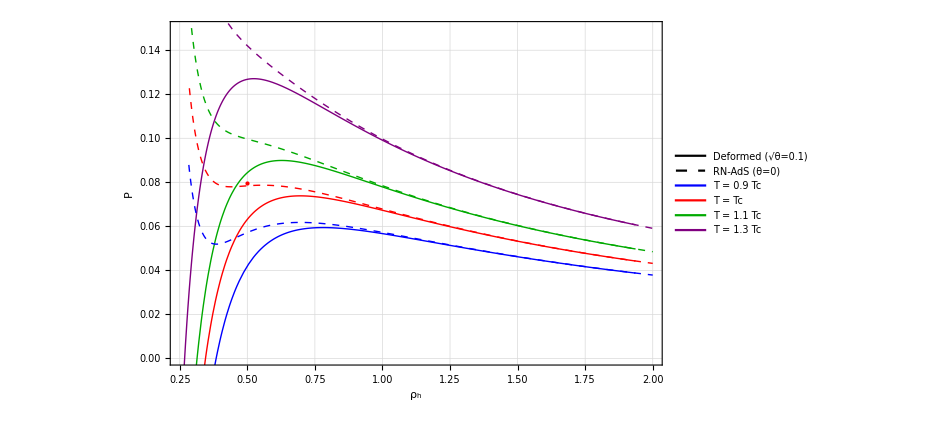

```mathematica
finalFig=Legended[Legended[figPV,Placed[legendStyle,{0.8,0.1}]],(*bas droite*)Placed[legendTemp,{0.9,0.8}](*haut droite*)]
```

```mathematica
Export["P_v_diagram.eps",finalFig,ImageResolution->1200]
```

P_v_diagram.eps